# Estimation of PP-tilting effect on hoppings

This was just a try to estimate how the PP-tilting would affect hoppings and therefore calculated current from analytical models.
Tip-orbital tilting is implemented in PP-STM for pd (tip - some of them)-sp (sample) orbitals, it doesn’t change the image much.

```mathematica
(*Not tilting, just moving up to 1Å, !!!!no normalization!!!!*)
```

```mathematica
const=1;const2=0.25;
Ass[x_]:=const;
Asz[x_]:=const;
Asx[x_]:=x*const;
Azz[x_]:=const;
Azx[x_]:=x*const-x*const2; 
Asdz2[x_]:=(1-0.5*x^2)*const;
Azdz2[x_]:=1(1-0.5*x^2)*const+Sqrt[3]*1*x^2*const2;
Axdz2[x_]:=x(1-0.5*x^2)*const+Sqrt[3]*1*x*const2;
```

```mathematica
styling={Automatic,Automatic,Automatic,Dashed,Dashed,DotDashed,DotDashed,DotDashed};
```

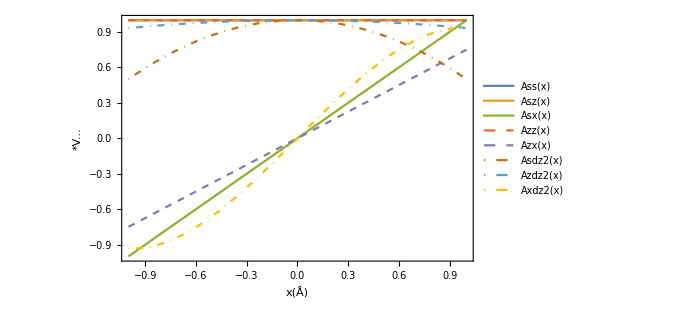

```mathematica
Plot[{Ass[x],Asz[x],Asx[x],Azz[x],Azx[x],Asdz2[x],Azdz2[x],Axdz2[x]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotStyle->styling]
```

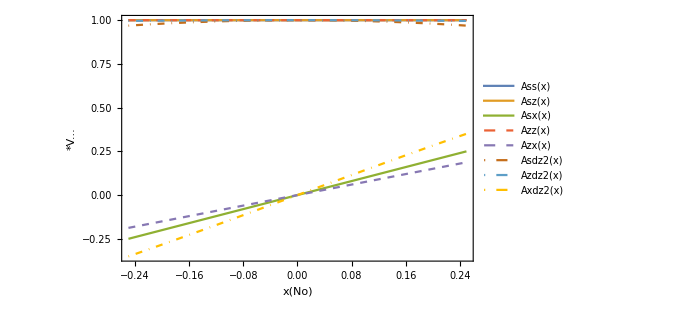

```mathematica
Plot[{Ass[x],Asz[x],Asx[x],Azz[x],Azx[x],Asdz2[x],Azdz2[x],Axdz2[x]},{x,-0.25,0.25},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[No],"*V..."},PlotStyle->styling]
```

```mathematica
(*Not tilting, just moving up to 1Å, *)
```

```mathematica
const=1;const2=0.25;
N0[x_,n0_]:=1/Sqrt[x^2+n0^2];
n[x_,n0_]:=n0*N0[x,n0];
Fss[x_,n0_]:=const;
Fsz[x_,n0_]:=n[x,n0]*const;
Fsx[x_,n0_]:=x*N0[x,n0]*const;
Fzz[x_,n0_]:=n[x,n0]^2*const+(1-n[x,n0]^2)*const2;
Fzx[x_,n0_]:=x*N0[x,n0]*n[x,n0]*const-x*N0[x,n0]*n[x,n0]*const2; 
Fsdz2[x_,n0_]:=(n[x,n0]^2-0.5*x^2*N0[x,n0]^2)*const;
Fzdz2[x_,n0_]:=n[x,n0](n[x,n0]^2-0.5*x^2*N0[x,n0]^2)*const+Sqrt[3]*n[x,n0]*x^2*N0[x,n0]^2*const2;
Fxdz2[x_,n0_]:=x(n[x,n0]^2-0.5*x^2*N0[x,n0]^2)*const+Sqrt[3]*n[x,n0]^2*x*const2;
```

20

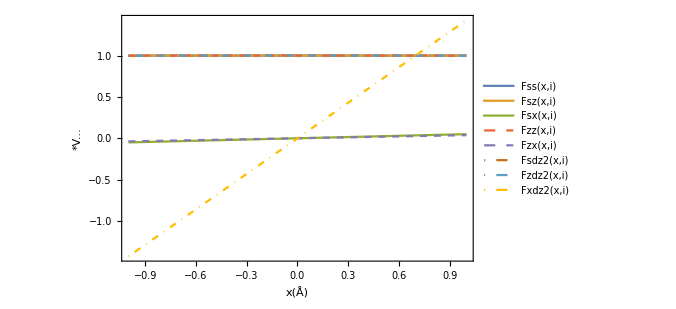

```mathematica
i=20
Plot[{Fss[x,i],Fsz[x,i],Fsx[x,i],Fzz[x,i],Fzx[x,i],Fsdz2[x,i],Fzdz2[x,i],Fxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotStyle->styling]
```

4.5

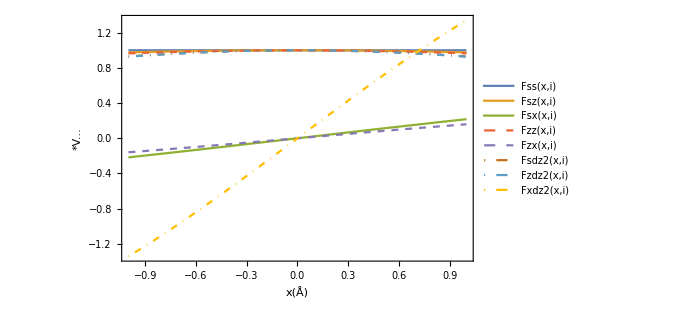

4.

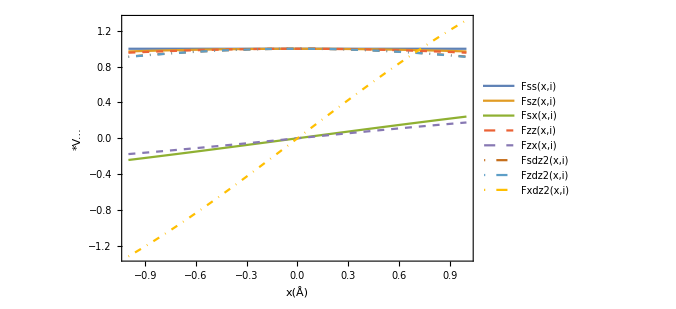

3.5

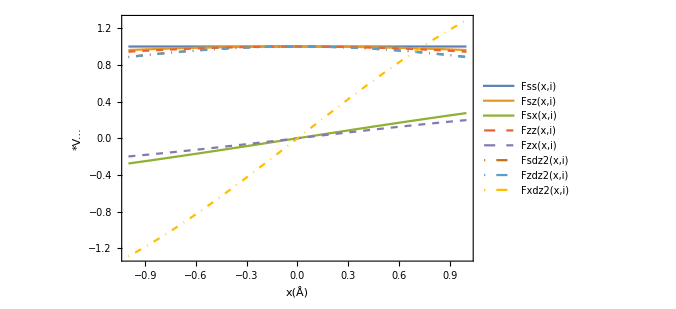

3.

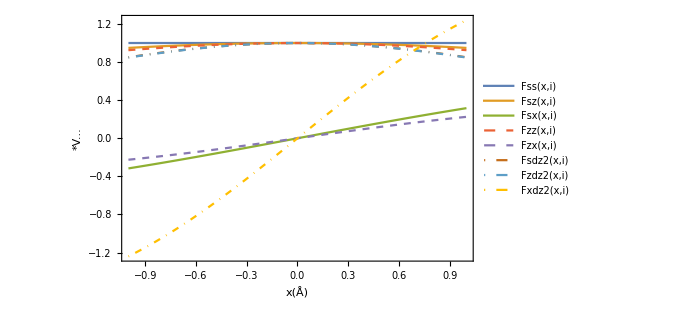

```mathematica
i=4.5
Plot[{Fss[x,i],Fsz[x,i],Fsx[x,i],Fzz[x,i],Fzx[x,i],Fsdz2[x,i],Fzdz2[x,i],Fxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotStyle->styling]
i=4.0
Plot[{Fss[x,i],Fsz[x,i],Fsx[x,i],Fzz[x,i],Fzx[x,i],Fsdz2[x,i],Fzdz2[x,i],Fxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotStyle->styling]
i=3.5
Plot[{Fss[x,i],Fsz[x,i],Fsx[x,i],Fzz[x,i],Fzx[x,i],Fsdz2[x,i],Fzdz2[x,i],Fxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotStyle->styling]
i=3.0
Plot[{Fss[x,i],Fsz[x,i],Fsx[x,i],Fzz[x,i],Fzx[x,i],Fsdz2[x,i],Fzdz2[x,i],Fxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotStyle->styling]
```

```mathematica
D[Fss[x,i],x]
D[Fsz[x,i],x]
D[Fsx[x,i],x]
D[Fzz[x,i],x]
D[Fzx[x,i],x]
D[Fsdz2[x,i],x]
D[Fzdz2[x,i],x]
D[Fxdz2[x,i],x]
```

```mathematica
dFss[x_,i_]:=0;
dFsz[x_,i_]:=-(3. x)/((9.+x^2)^(3/2));
dFsx[x_,i_]:=-x^2/((9.+x^2)^(3/2))+1/(√(9.0+x^2));
dFzz[x_,i_]:=-(13.5 x)/((9.+x^2)^2);
dFzx[x_,i_]:=-(4.5 x^2)/((9.+x^2)^2)+2.25/(9.+x^2);
dFsdz2[x_,i_]:=-(18. x)/((9.+x^2)^2)+(1. x^3)/((9.+x^2)^2)-(1. x)/(9.+x^2);
dFzdz2[x_,i_]:=-(3.897114317029974 x^3)/((9.+x^2)^(5/2))+(2.598076211353316 x)/((9.+x^2)^(3/2))+(3. (-(18. x)/((9.+x^2)^2)+(1. x^3)/((9.+x^2)^2)-(1. x)/(9.+x^2)))/(√(9.+x^2))-(3. x (9./(9.+x^2)-(0.5 x^2)/(9.+x^2)))/((9.+x^2)^(3/2));
dFxdz2[x_,i_]:=-(7.794228634059947 x^2)/((9.+x^2)^2)+12.897114317029974/(9.+x^2)-(0.5 x^2)/(9.+x^2)+x (-(18. x)/((9.+x^2)^2)+(1. x^3)/((9.+x^2)^2)-(1. x)/(9.+x^2));
```

4.5

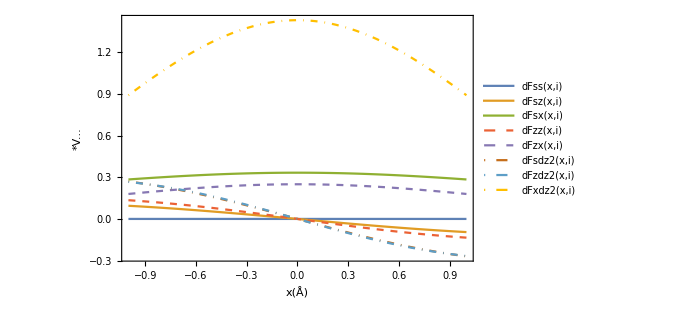

4.

-Graphics-

3.5

-Graphics-

3.

-Graphics-

```mathematica
i=4.5
Plot[{dFss[x,i],dFsz[x,i],dFsx[x,i],dFzz[x,i],dFzx[x,i],dFsdz2[x,i],dFzdz2[x,i],dFxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotRange->Full,PlotStyle->styling]
i=4.0
Plot[{dFss[x,i],dFsz[x,i],dFsx[x,i],dFzz[x,i],dFzx[x,i],dFsdz2[x,i],dFzdz2[x,i],dFxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotRange->Full,PlotStyle->styling]
i=3.5
Plot[{dFss[x,i],dFsz[x,i],dFsx[x,i],dFzz[x,i],dFzx[x,i],dFsdz2[x,i],dFzdz2[x,i],dFxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotRange->Full,PlotStyle->styling]
i=3.0
Plot[{dFss[x,i],dFsz[x,i],dFsx[x,i],dFzz[x,i],dFzx[x,i],dFsdz2[x,i],dFzdz2[x,i],dFxdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotRange->Full,PlotStyle->styling]
```

```mathematica
xang[θ_]:=4*Sin[θ*Degree]
```

4.5

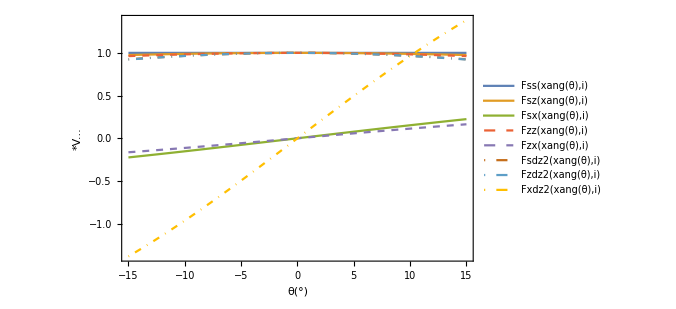

4.

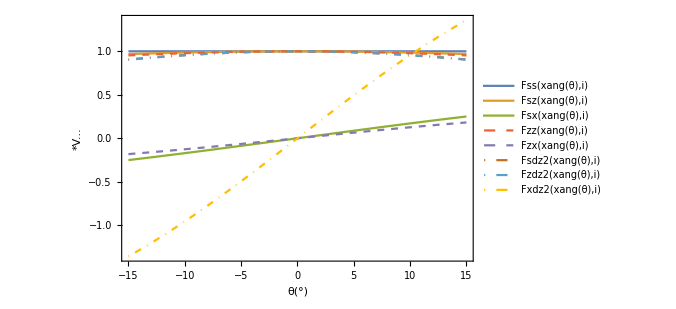

3.5

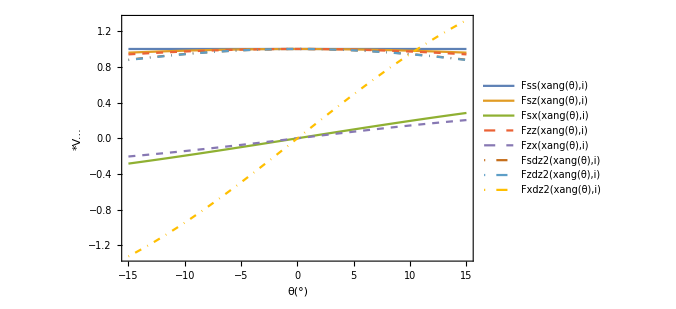

3.

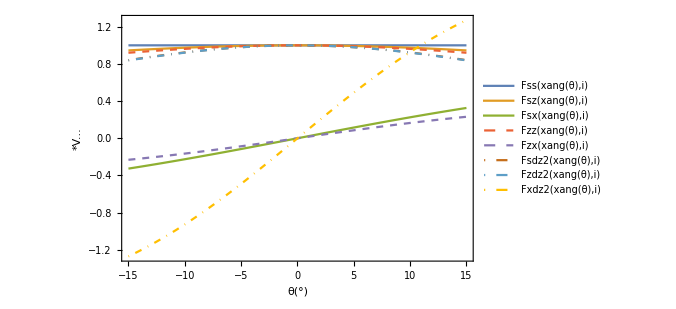

```mathematica
i=4.5
Plot[{Fss[xang[θ],i],Fsz[xang[θ],i],Fsx[xang[θ],i],Fzz[xang[θ],i],Fzx[xang[θ],i],Fsdz2[xang[θ],i],Fzdz2[xang[θ],i],Fxdz2[xang[θ],i]},{θ,-15,15},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{θ[°],"*V..."},PlotStyle->styling]
i=4.0
Plot[{Fss[xang[θ],i],Fsz[xang[θ],i],Fsx[xang[θ],i],Fzz[xang[θ],i],Fzx[xang[θ],i],Fsdz2[xang[θ],i],Fzdz2[xang[θ],i],Fxdz2[xang[θ],i]},{θ,-15,15},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{θ[°],"*V..."},PlotStyle->styling]
i=3.5
Plot[{Fss[xang[θ],i],Fsz[xang[θ],i],Fsx[xang[θ],i],Fzz[xang[θ],i],Fzx[xang[θ],i],Fsdz2[xang[θ],i],Fzdz2[xang[θ],i],Fxdz2[xang[θ],i]},{θ,-15,15},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{θ[°],"*V..."},PlotStyle->styling]
i=3.0
Plot[{Fss[xang[θ],i],Fsz[xang[θ],i],Fsx[xang[θ],i],Fzz[xang[θ],i],Fzx[xang[θ],i],Fsdz2[xang[θ],i],Fzdz2[xang[θ],i],Fxdz2[xang[θ],i]},{θ,-15,15},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{θ[°],"*V..."},PlotStyle->styling]
```

```mathematica
(*Tilting PP, not orbitals, V don't depend on distance*)
```

```mathematica
const=1;const2=0.25;l0=4;
ni[x_,n0_]:=(n0+l0-Sqrt[l0^2-x^2])/Sqrt[(n0+l0-Sqrt[l0^2-x^2])^2+x^2];
xi[x_,n0_]:=x/Sqrt[(n0+l0-Sqrt[l0^2-x^2])^2+x^2];
Ess[x_,n0_]:=const;
Esz[x_,n0_]:=ni[x,n0]const;
Esx[x_,n0_]:=xi[x,n0]const;
Ezz[x_,n0_]:=(ni[x,n0])^2*const+(1-(ni[x,n0])^2)*const2;
Ezx[x_,n0_]:=xi[x,n0]*ni[x,n0]const-xi[x,n0]*ni[x,n0]const2; 
Esdz2[x_,n0_]:=((ni[x,n0])^2-0.5*xi[x,n0]^2)*const;
Ezdz2[x_,n0_]:=ni[x,n0](ni[x,n0]^2-0.5*xi[x,n0]^2)*const+Sqrt[3]*ni[x,n0]*xi[x,n0]^2*const2;
Exdz2[x_,n0_]:=xi[x,n0](ni[x,n0]^2-0.5*xi[x,n0]^2)*const+Sqrt[3]*ni[x,n0]^2*xi[x,n0]*const2;
```

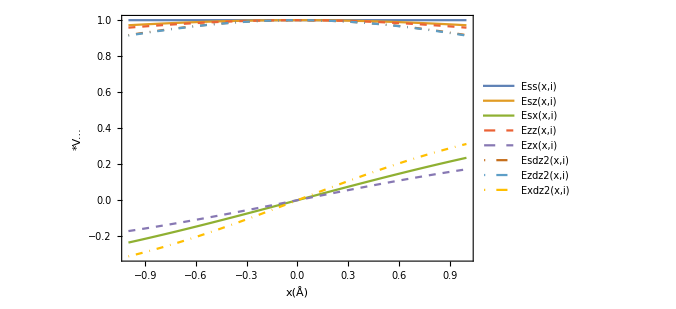

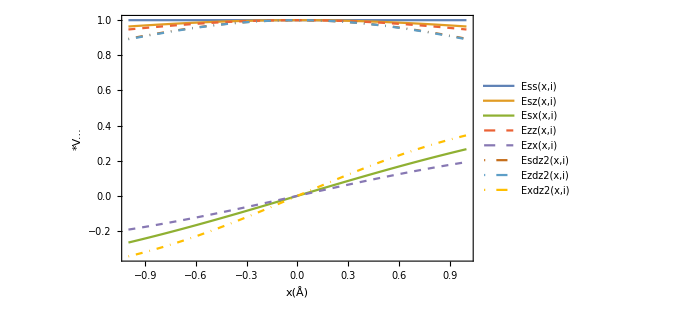

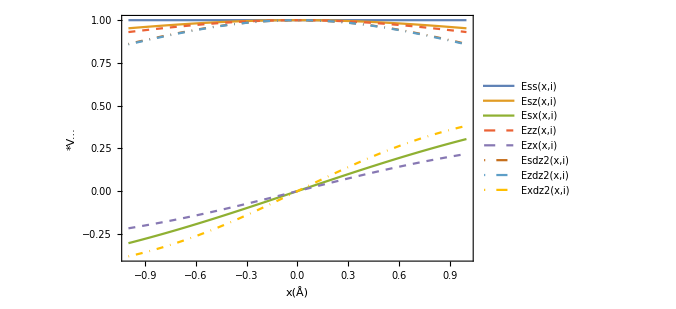

```mathematica
i=4;
Plot[{Ess[x,i],Esz[x,i],Esx[x,i],Ezz[x,i],Ezx[x,i],Esdz2[x,i],Ezdz2[x,i],Exdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotRange->Full,PlotStyle->styling]
i=3.5;
Plot[{Ess[x,i],Esz[x,i],Esx[x,i],Ezz[x,i],Ezx[x,i],Esdz2[x,i],Ezdz2[x,i],Exdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotRange->Full,PlotStyle->styling]
i=3.0;
Plot[{Ess[x,i],Esz[x,i],Esx[x,i],Ezz[x,i],Ezx[x,i],Esdz2[x,i],Ezdz2[x,i],Exdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotRange->Full,PlotStyle->styling]
```

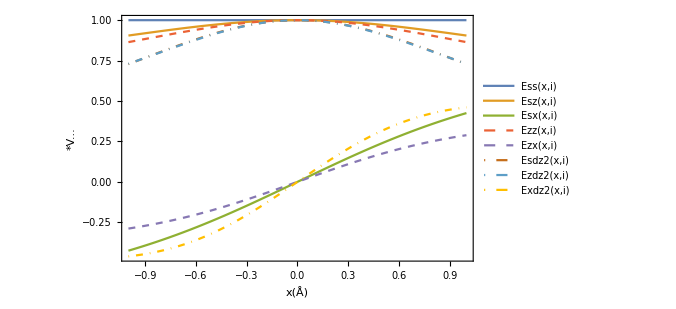

```mathematica
i=2.0;
Plot[{Ess[x,i],Esz[x,i],Esx[x,i],Ezz[x,i],Ezx[x,i],Esdz2[x,i],Ezdz2[x,i],Exdz2[x,i]},{x,-1,1},PlotLegends->"Expressions",ImageSize->500,Frame->True,FrameLabel->{x[Å],"*V..."},PlotRange->Full,PlotStyle->styling]
```